```mathematica
Remove["Global`*"]
```

```mathematica
V=0.001;
ρ=6.022*10^28;
θD=428;
kB=1.38064852*10^-23;
```

```mathematica
f[x_]:=(x^4*Exp[x])/(Exp[x]-1)^2
```

```mathematica
cv[T_]:=(9*V*ρ*kB*(T/θD)^3)*Integrate[f[x],{x,0,θD/T}]
```

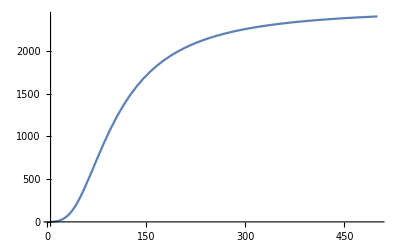

```mathematica
Plot[cv[T],{T,5,500}]
```